# Exercise 5

As with all of the exercises you will complete in this course, you will be expected to turn your *.nb file in to the course TA before the next lecture.  Please do so by e-mailing your completed exercise file to Lan Yu (ece329.uiuc@gmail.com), make sure you name the file using the following notation: “Exn_Last_First.nb”, where n is the Exercise number (in this case, 5), and First and Last would be your first and last name.  So my submission to Lan for this exercise would be titled “Ex5_Wasserman_Dan.nb”.  You will receive full credit for your exercise if it turned in before the next lecture (Lecture n+1).  No late submissions will be accepted.

## Objective/Overview:

In today’s exercise, we will practice taking the Gradient of Scalar fields.  We will show that that Curl-free fields have path-independent line integrals of Electric field.

```mathematica
ClearAll[vxy,v1, e1, gradvxy, vxyz, gradvxyz, curlgradvxyz]
```

## The Gradient

The final del-operation we cover in class is the Gradient.  The gradient operates on a scalar field, NOT a vector field.  The Gradient, however, returns a vector field that points in the direction which the scalar field is changing, with a magnitude telling us how fast the field is changing. Let’s define a scalar field:

```mathematica
vxy=Exp[-(x^2/.5^2)]*Exp[-(y^2/.5^2)]
```

ⅇ^(-4. x^2-4. y^2)

```mathematica
Plot3D[vxy,{x,-1,1},{y,-1,1}, PlotRange->Full]
```

-Graphics3D-

This is a 2D Gaussian distribution, but it basically gives us a hill, so we can fairly quickly imagine what the gradient of this function will look like.  Let’s see if we are right:

```mathematica
gradvxy=Grad[vxy,{x,y}]
```

{-8. ⅇ^(-4. x^2-4. y^2) x,-8. ⅇ^(-4. x^2-4. y^2) y}

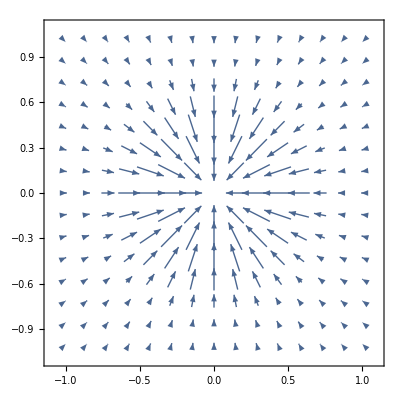

```mathematica
VectorPlot[gradvxy,{x,-1,1},{y,-1,1}]
```

If we want to be super-cool, we can superimpose the vector field on the 2D surface from before...

```mathematica
Plot3D[vxy,{x,-1,1},{y,-1,1}, PlotRange->Full, PlotStyle->Texture[StreamPlot[gradvxy,{x,-1,1},{y,-1,1}]]]
```

-Graphics3D-

You can see that the Gradient gives us us a vector field that points along the slope of our surface.  This is harder (if not impossible) to picture in three dimensions, of course, but the basic concepts are the same.

## The Electrostatic Potential

We can think of the electrostatic potential “V” as the potential energy of a test charge of +1C in an electric field E⃗=-∇V.  In other words, the (negtive) gradient of the electrostatic potential gives us the Electric Field.
We have already found the electric field for our “vxy” above, since it is just the gradient of “vxy”.  Let’s make sure that this is, in fact a Curl-free field:

```mathematica
curlEgaussian=Curl[gradvxy,{x,y}]
```

0.

Remember, the curl of a vector field should be another vector field.  However, when we have a 2D vector field, like the one above, then the curl will ALWAYS be orthogonal to our field vectors.  So forthe field above, all vectors are in the xy plane, and therefore the curl is in z.  That is why Mathematica gives the curl of a 2D field as a scalar number...

Below, create a scalar potential in 3D!  Construct the Electric Field associated with this scalar potential (and plot it) and show that this is a Curl-free electric field:

```mathematica
vxyz=3x*y^2+Cos[z]/z
```

3 x y^2+Cos[z]/z

```mathematica
gradvxyz=Grad[vxyz,{x,y,z}]
```

{3 y^2,6 x y,-Cos[z]/z^2-Sin[z]/z}

```mathematica
VectorPlot3D[gradvxyz,{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

```mathematica
curlgradvxyz=Curl[gradvxyz,{x,y,z}]
```

{0,0,0}

For an Electrostatic Field, the Curl is always zero, and we can always write the electrostatic field as the Gradient of a scalar potential (as you just showed!).

## Path Independence

One of the consequences of an Electrostatic field is that the line integral of the field between two points will always be the same, regardless of the path that you take between those two points.  This is related to conservation of energy, which we will get to later on.  For now, let’s create a new Electric Field from the gradient of a scalar:

```mathematica
v1=x^2*z-y^3*z
```

x^2 z-y^3 z

```mathematica
e1=Grad[v1,{x,y,z}]
```

{2 x z,-3 y^2 z,x^2-y^3}

```mathematica
p1=VectorPlot3D[e1,{x,-2,2},{y,-2,2},{z,-2,2}]
```

-Graphics3D-

OK.  Now we want to show that the line integral ∫_a^b OverVector[e1]·ⅆ ℓ⃗ is the same regardless of the path we take.  Lets say our two points are:  a=(0,0,0) and b=(2,2,2).
We can try a number of paths, but let’s start by integrating along three lines: from (0,0,0)->(2,0,0), (2,0,0)->(2,2,0), and (2,2,0)->(2,2,2):

```mathematica
p2=Graphics3D[{Red,Thick,Line[{{0,0,0},{2,0,0},{2,2,0},{2,2,2}}]}];
Show[p1,p2]
```

-Graphics3D-

Let’s write our vector field as a function:

```mathematica
fe1[x_,y_,z_]:={2 x z,-3 y^2 z,x^2-y^3}
```

```mathematica
Integrate[Dot[fe1[x,0,0],{1,0,0}],{x,0,2}]
```

0

```mathematica
Integrate[Dot[fe1[2,y,0],{0,1,0}],{y,0,2}]
```

0

```mathematica
Integrate[Dot[fe1[2,2,z],{0,0,z}],{z,0,2}]
```

-8

So the line integral of the electric field over the three lines connecting {0,0,0} to {2,2,2} gives us “-8”.  I want to show you one more way of taking a line integral before you try it yourself.  In the next section, we are going to parameterize the path.  First we create a function to describe our electric field, then we design a path:

```mathematica
fe1[x_,y_,z_]:={2 x z,-3 y^2 z,x^2-y^3}  ;
path1[t_]:={2*t,2*Sin[5*t*Pi/2],2*t^2}  (*This clearly gives us, for t=0, {0,0,0] and for t=1, {2,2,2}*)
```

To plot this, we can use a Parametric Plot:

```mathematica
p3=ParametricPlot3D[path1[t],{t,0,1},PlotStyle->Red];
```

```mathematica
Show[p1,p3]
```

-Graphics3D-

The line integral is then our function written in terms of “t”, dotted with t’, integrated between 0<t<1. Mathematically, what we have done here is:
E⃗={E_x(x,y,z),E_y(x,y,z),E_z(x,y,z)}, 
{x,y,z}={x(t),y(t),z(t)}
∫_(0,0,0)^(2,2,2) E⃗·d l⃗=∫_(t=0)^(t=1) E⃗(x(t),y(t),z(t))·((dx(t))/dt,(dy(t))/dt,(dz(t))/dt)
Please bear in mind that “t” does not necessarily stand for time (though I guess it could if you wanted to think of it that way)

Let’s see how this works:

```mathematica
Integrate[Dot[fe1[2*t,2*Sin[5*t*Pi/2],2*t^2],path1'[t]], {t,0,1}]
```

-8

OK, now you describe a path from {0,0,0} to {2,2,2}, and take the line integral of this path through the vector field “e1”.  You can do this piecewise, with lines, or by creating a parameterized path.  What do you get?

```mathematica
path2[t_]:={2*t^2,2*t,2*Sin[t*Pi/2]}  (*This clearly gives us, for t=0, {0,0,0] and for t=1, {2,2,2}*)
```

```mathematica
ptest=ParametricPlot3D[path2[t],{t,0,1},PlotStyle->Red];
```

```mathematica
Show[p1,ptest]
```

-Graphics3D-

```mathematica
Integrate[Dot[fe1[2*t^2,2*t,2*Sin[t*Pi/2]],path2'[t]], {t,0,1}]
```

-8

Hopefully you also got “-8”.  What happens if you go in the opposite direction?

```mathematica
Integrate[Dot[fe1[2*t^2,2*t,2*Sin[t*Pi/2]],path2'[t]], {t,1,0}]
```

8

This makes sense!  If you go from point “a” to “b” in a static Electric Field and your electrostatic potential decreases by 8, then when you go back to point “a” from “b”, you would expect your electrostatic potential to increase by 8!!  This tells us that the field is Conservative.  As you make a round trip, along any path, you will never gain (or lose) energy from the Electrostatic Field...total energy is conserved.
Let’s  create a round trip path:

```mathematica
path3[t_]:={Sin[2*Pi*t]*Cos[2*Pi*t],Sin[6*t*Pi],1-(2*t-1)^2}  (*This clearly gives us, for t=0, {0,0,0] and for t=1, {0,0,0}*)
```

To plot this, we can use a Parametric Plot:

```mathematica
p4=ParametricPlot3D[path3[t],{t,0,1},PlotStyle->Red];
```

```mathematica
p5=Animate[Graphics3D[Sphere[{Sin[2*Pi*t]*Cos[2*Pi*t],Sin[6*t*Pi],1-(2*t-1)^2},0.2],PlotRange->{{-2,2},{-2,2},{-2,2}}],{t,0,1},AnimationRepetitions->1] (*just for fun...*)
```

```mathematica
Show[p1,p4]
```

-Graphics3D-

If we integrate along this entire path (essentially from t=0 to t=1), we get:

```mathematica
Integrate[Dot[fe1[Sin[2*Pi*t]*Cos[2*Pi*t],Sin[6*t*Pi],1-(2*t-1)^2],path3'[t]], {t,0,1}]
```

0

So we are able to create some totally crazy loop, integrate the dot product of the Electric Field and a differential element of the path over the entire path, and as long as the field is curl-free (conservative), we will always get zero!!
To hammer this home, let’s go back to our Elecrostatic Potential:

```mathematica
fv1[x_,y_,z_]:=x^2*z-y^3*z
```

Solve for the Electrostatic Potential at {0,0,0} and {2,2,2}.  What do you notice?

```mathematica
fv1[2,2,2]
```

-8

```mathematica
fv1[0,0,0]
```

0

The potential difference, of course, is equivalent to the path integral between those two points!